```mathematica
(* 2.2a*)
(*Give Subscript[θ, 0] in terms of(g,l,γ,m)*)

(* From the task:
θ^(..) = -g/l*sin(θ) - γ/m*θ̇;
By substitution ω = θ̇; and the equations θ = Subscript[θ, 0]*x; ω = Subscript[ω, 0]*y; t = Subscript[t, 0] t';
We obtain:
dx/dt' = y; dy/dt' = -sin(x)-σ*y;

Start by computing Subscript[θ, 0];
ω = θ̇ <-> Subscript[ω, 0]*y = Subscript[θ, 0]/Subscript[t, 0]*dx/dt';
dx/dt' = Subscript[t, 0]/Subscript[θ, 0]*Subscript[ω, 0]*y;
The similarities from dx/dt' = y; we can conclude that:
(Subscript[t, 0] Subscript[w, 0])/Subscript[θ, 0] = 1;
-> Subscript[θ, 0]= Subscript[t, 0] Subscript[w, 0];
Start calulating 2.2b and 2.2c and come back and insert the values.
-> Subscript[θ, 0]= Subscript[t, 0] Subscript[w, 0]=√(g/l)*√(l/g)=1;

(* 2.2b*)
(*Give Subscript[ω, 0] in terms of(g,l,γ,m)*)
Rewriting the main function and set θ^(..) = ω̇, thus:

ω̇ = -g/l*sin(Subscript[θ, 0]*x) - γ/m*Subscript[w, 0]*y;
Where ω̇ = Subscript[ω, 0]/Subscript[t, 0]*dy/dt'; 
By inserting and rewriting we obtain:
dy/dt' = -Subscript[t, 0]/Subscript[ω, 0]*g/l*sin(Subscript[θ, 0]*x) - Subscript[t, 0]/Subscript[ω, 0]*γ/m*Subscript[w, 0]*y;
The similarities from dy/dt' = -sin(x)-σ*y; we can conclude that:
Subscript[θ, 0] = 1; and Subscript[t, 0]/Subscript[ω, 0]*g/l = 1;
and by combaning the eqs above and inserting Subscript[θ, 0] = 1 in Subscript[θ, 0]= Subscript[t, 0] Subscript[w, 0]; we obtain:
-> Subscript[ω, 0] = √(g/l); 

(* 2.2c*)
(*Give Subscript[t, 0] in terms of(g,l,γ,m)*)
With the same equations calculated in 2.2b and inserting Subscript[θ, 0] = 1 in Subscript[θ, 0]= Subscript[t, 0] Subscript[w, 0]; we obtain:
-> Subscript[t, 0] = √(l/g);

(* 2.2d*)
(*Give σ  in terms of(g,l,γ,m)*)
Now from the second term we can compute σ:
Subscript[t, 0]/Subscript[ω, 0]*γ/m*Subscript[w, 0]*y is similar to σ*y;

We can insert the computed Subscript[t, 0] in combination with eliminating Subscript[w, 0]:
-> σ = √(l/g)*γ/m
*)

(* 2.2e *)
(* For arbitrary σ ≥ 0, calculate and classify the fixed points as a function of σ*)
(* From the task: 
dx/dt' = 0 -> y -> 0 and  dy/dt' = 0 ->  -sin(x)-σ*0 = 0;
we then obatin that x = nπ -> the fixed is at (nπ, 0) -> investigate it's eigenvalues*)
M = Grad[{y, -Sin[x]-σ*y}, {x, y}];
eig = Eigenvalues[M];
(*n=1, odd number*)
eig/. x-> π
```

{1/2 (-σ-√(4+σ^2)),1/2 (-σ+√(4+σ^2))}

```mathematica
(*n=2, even number*)
eig/. x-> 2π
```

{1/2 (-σ-√(-4+σ^2)),1/2 (-σ+√(-4+σ^2))}

```mathematica
(*For n=2 and σ ≥ 2*)
eig/. {x-> 2π, σ -> 3}
```

{1/2 (-3-√5),1/2 (-3+√5)}

```mathematica
(* For odd n -> theterm under the root will always be greater than the term outside. ->Subscript[λ, 1] will be negative while Subscript[λ, 2] will be positive -> saddle-point*)
(* For even n -> term under the root will always be smaller than the other term. -> both Subscript[λ, 1,2] will be negative for σ ≥ 0. *)
(*When σ ≥ 2 -> stable real values under the root. When σ < 2 -> imaginary values under the root. *)
(* We can imagine for the case 2x2 where left side -> σ < 2, right side -> σ > 2,top half -> for odd n and bottom half -> for even n. The classification would then be ->[[Saddle, Saddle], [Stable with oscillation, Stable]] *)
(*See fixed points evaluated with Solve*)
xDot[x_,y_,σ_]:=y
yDot[x_,y_,σ_]:=-Sin[x]-σ y
Solve[{xDot[x,y,σ] == 0, yDot[x,y,σ]==0}]
```

{{y→0,x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{y→0,x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

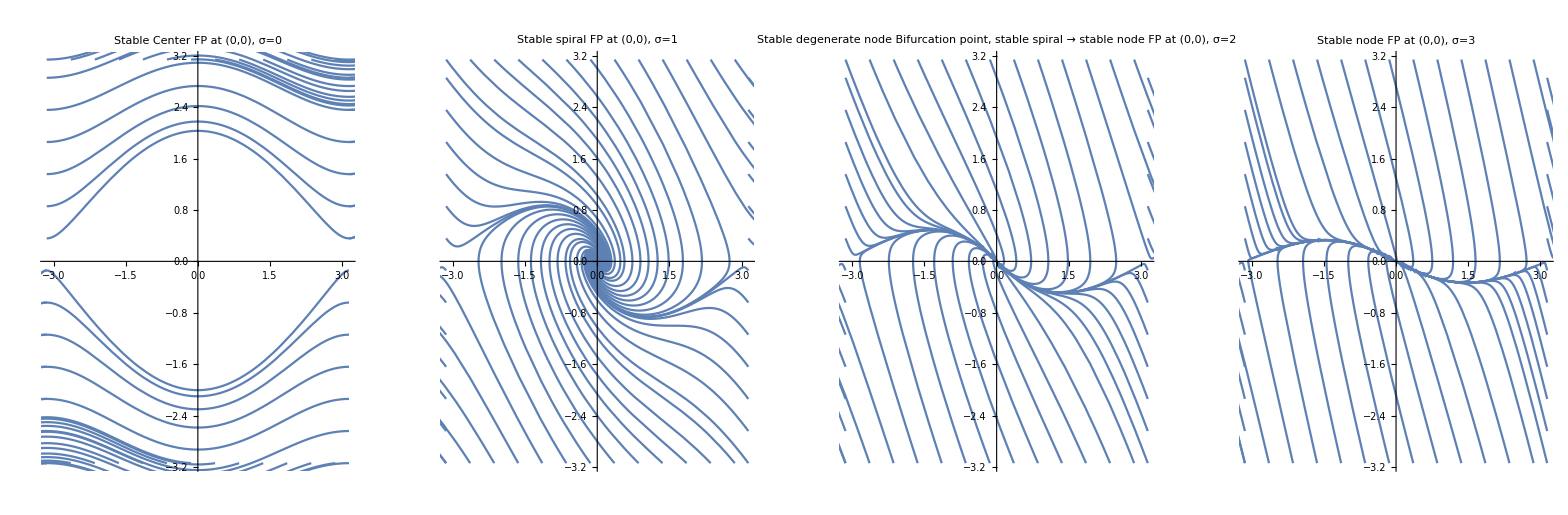

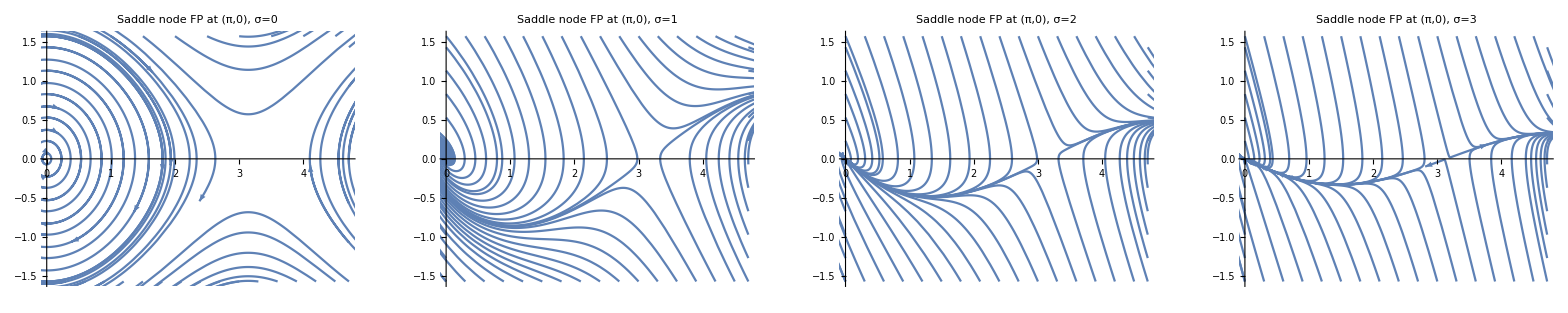

```mathematica
(*Plot with different values on σ, the values = 0,1,2,3 *)
minx=-π;miny=-π;maxx=π;maxy=π;
sol1[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{0}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p1=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol1[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Stable Center\nFP at (0,0), σ=0"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol2[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{1}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p2=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol2[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Stable spiral\nFP at (0,0), σ=1"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol3[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{2}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p3=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol3[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Stable degenerate node\nBifurcation point, stable spiral → stable node\nFP at (0,0), σ=2"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol4[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{3}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.5}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.5}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p4=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol4[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Stable node\nFP at (0,0), σ=3"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];

minx=0;miny=-π/2;maxx=π*3/2;maxy=π/2;
sol5[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{0}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.5}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.5}]];
p5=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol5[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10},PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Saddle node\nFP at (π,0), σ=0"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol6[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{1}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p6=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol6[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Saddle node\nFP at (π,0), σ=1"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol7[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{2}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p7=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol7[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10}, PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Saddle node\nFP at (π,0), σ=2"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
sol8[x0_,y0_]:=Table[NDSolve[{D[x[t],t]==y[t], D[y[t],t]==-Sin[x[t]]-σ y[t],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,0,10}],{σ,{3}}];
initialConditions=Join[Table[{minx,y},{y,miny,maxy,0.3}],Table[{maxx,y},{y,miny,maxy,0.3}],Table[{x,miny},{x,minx,maxx,0.3}],Table[{x,maxy},{x,minx,maxx,0.3}]];
p8=Show[Table[ParametricPlot[Evaluate[{x[t],y[t]}/.sol8[initialConditions[[i,1]],initialConditions[[i,2]]]],{t,0,10},PlotRange->{{minx, maxx}, {miny, maxy}},
PlotLabel->"Saddle node\nFP at (π,0), σ=3"]/.Line[x_]:>{Arrowheads[{0,0.04,0.04,0.04,0}],Arrow[x]},{i,Length[initialConditions]}]];
GraphicsRow[{p1,p2,p3,p4}, ImageSize->Full]
GraphicsRow[{p5,p6,p7,p8}, ImageSize->Full]
```

```mathematica
(* 2.2f *)
(*Derive an integral of motion for this dynamical system in terms of(ϕ,ω,τ)*)
(*From the task:
ϕ̇ = ω; and ω̇ = sin(ϕ)[cos(ϕ)-τ-1];

Rewrite as ODE with ϕ^(..) = ω̇ and inserting it to the second term;
ϕ^(..) = sin(ϕ)[cos(ϕ)-τ-1] -> ϕ^(..) - sin(ϕ)[cos(ϕ)-τ-1] = 0;

Multiply both sides by dϕ/dt;
dϕ/dt(d^2 ϕ)/dt^2 - dϕ/dt(sin(ϕ)[cos(ϕ)-τ-1]) = 0;

One can integrate twice(followed an example from the book);
1/2 d/dt((dϕ/dt))^2 - d/dt(sin(ϕ)[cos(ϕ)-τ-1])dϕ = 0; -> d/dt(ω^2 - ∫2sin(ϕ)[cos(ϕ)-τ-1] dϕ) = 0; -> ω^2 - cos(ϕ)(-2(1+τ)+cos(ϕ)) + c = 0;

With ω -> 0 and ϕ -> π/2 we want -1 -> c = -1; We can now combine and put together the final expression:

Derive an integral of motion -> = -1 ω^2 - cos(ϕ)*(-2*(1+τ)+cos(ϕ));
 *)

Integrate[-2Sin[ϕ]*(Cos[ϕ]-τ-1), ϕ]//FullSimplify;
ω^2+Cos[ϕ]*(-2*(1+τ)+Cos[ϕ])+c /. {ω-> 0, ϕ-> π/2, c-> -1};
ω^2+Cos[ϕ]*(-2*(1+τ)+Cos[ϕ])-1
```

-1+ω^2+Cos[ϕ] (-2 (1+τ)+Cos[ϕ])